# Lecture 11 Mathematica Symbolic Expressions and List

A famous saying goes “Everything  in Wolfram Language is a symbolic expressions”. This central concept is just like “array” in Matlab and “object” in Python. We start with an overview of “symbolic expression” concept in Mathematica, and then focus on the most basic and important type of symbolic expressions -- Lists.

## Concepts of Symbolic Expressions

Symbolic expression in Mathematica is defined in a recursive way (composite of functions): Every expression  can be written as head[part1, part2, part2], where part can be other expressions.

### Head, FullForm and TreeForm

```mathematica
x+y
```

```mathematica
FullForm[x+y]
```

```mathematica
Head[x+y]
```

```mathematica
FullForm[a b+c] (*note the space between ab*)
```

```mathematica
FullForm[a/b]
```

```mathematica
FullForm[1+2*3] (*will not display fullform you expected -- evaluation comes first*)
```

```mathematica
FullForm[Hold[1+2*3]] (*Hold will prevent evaluation*)
```

```mathematica
myList = {1,2,3}
```

```mathematica
FullForm[myList]
```

```mathematica
img = -Graphics-
```

```mathematica
FullForm[img]
```

```mathematica
Head[img]
```

```mathematica
FullForm[1/(a+b) x^2]
```

```mathematica
TreeForm[1/(a+b) x^2]
```

```mathematica
tree = TreeForm[myList]
```

```mathematica
Head[tree]
```

```mathematica
TreeForm
```

```mathematica
FullForm[tree]
```

```mathematica
TreeForm[tree]
```

graph = WolframAlphaQueryParseResults

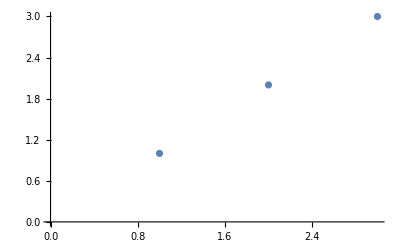

```mathematica
Head[graph]
```

```mathematica
g = Graphics[{Orange,Disk[{0,0}],Opacity[.7],Pink,Disk[{1,0}]}]
```

```mathematica
TreeForm[g]
```

Atomatic Object

Atom object is the “leaf” in the treeform: they cannot be decomposed further, and its fullform is itself. Its head actually tells its data type.

```mathematica
FullForm[a]
```

```mathematica
Head[a]
```

```mathematica
Head[2]
```

```mathematica
Head[2.0]
```

```mathematica
Head[1/2]
```

```mathematica
AtomQ[3] (*whether the expresssion is atom or not*)
```

```mathematica
AtomQ[{1,2,3}]
```

```mathematica
False
```

```mathematica
Head[Pi]
```

```mathematica
AtomQ[Pi]
```

```mathematica
N[Pi]
```

## List in Mathematica

### List Creation: Direct Input with {} (List), Range, Table

```mathematica
myList = {3, 4, 5, 7/8, x, y, x^2 + 3 y^3, {a, b,c}}
```

```mathematica
TreeForm[myList]
```

```mathematica
myList = List[3,4,5] (*equivalent to {3,4,5}*)
```

```mathematica
?Range
```

```mathematica
l= Range[1,20,2]
```

```mathematica
Head[l]
```

```mathematica
l1 =Range[x,x+4] (*always remember Mathematica can do the symbolic*)
```

```mathematica
TreeForm[l1]
```

```mathematica
?Table
```

```mathematica
Table[5,10]
```

```mathematica
Table[2,10]
```

```mathematica
Table[f[n],{n,10}]
```

```mathematica
Table[n^2,{n,2,20,3}]
```

```mathematica
Table[Range[n],{n,5}]
```

```mathematica
Table[Prime[i],{i,100}]
```

```mathematica
?Prime
```

### Extracting Elements in List: Indexing and Slicing

```mathematica
FullForm[Hold[l1[[2]]]]
```

```mathematica
l1[[2]] (*note the double bracket here*)
```

```mathematica
Part[l1,2] (*the equivalent way*)
```

```mathematica
l1[[-1]](*the last element*)
```

```mathematica
l = Range[1,100,2]
```

```mathematica
l[[{2,4}]]
```

```mathematica
?;;
```

```mathematica
l[[2;;-1;;2]]
```

```mathematica
FullForm[1;;6;;2] (*the simple form of indexing and slicing are in general called "syntactic sugar" in programming language *)
```

### Manipulating List: Append and Join

```mathematica
l = {1,2,3};
l = Append[l,x]
```

```mathematica
l1 = {a,b,c};
l2 = {4,5,6};
Join[l1,l2]
```

```mathematica
Operations on List
```

```mathematica
{1,2,3}+1
```

```mathematica
{a,b,c}+d
```

```mathematica
Log[l] (*elementwise, or in Mathematica it is called 'listable'*)
```

```mathematica
N[%]
```

```mathematica
Attributes[Log]
```